0.5-3. x

{2.5,-7.5}

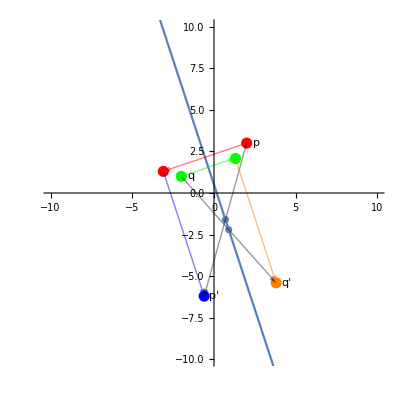

```mathematica
(*Glide Reflection Project: Jatin Kohli P5*)
linearReflection =  
Function[
{point,m,b},
1/(1+m^2)*{(1-m^2)*point[[1]]+2*m*point[[2]]-2*m*b,(m^2-1)*point[[2]]+2*m*point[[1]]+2*b}
];

p = {2,3}; (*Original point 1*)
q={-2,1};  (*Original point 2*)
pPrime={-0.6,-6.2}; (*Final point 1*)
qPrime={3.8,-5.4};(*Final point 2*)

midpoints = {(pPrime+p)/2,(qPrime+q)/2};

slope =( midpoints[[1]][[2]]-midpoints[[2]][[2]])/(midpoints[[1]][[1]]-midpoints[[2]][[1]]); (*m = (Subscript[y, 1]-Subscript[y, 2])/(Subscript[x, 1]-Subscript[x, 2])*)
b=midpoints[[2]][[2]]-slope*midpoints[[2]][[1]]; (*b = y - mx*)
reflectionLine [x_]=slope*x + b;

reflectedP =linearReflection[p,slope,b];
glideVectorP = {reflectedP,pPrime};
reflectedQ =linearReflection[q,slope,b];
glideVectorQ = {reflectedQ,qPrime};

reflectionLine[x] (*Print reflection line*)
pPrime -reflectedP (*Print glide vector*)

Show[
Graphics[Prepend[Riffle[{Red,Green,Blue,Orange},Point/@{p,q,pPrime,qPrime}],PointSize[.02]],PlotRange-> {{-10,10},{-10,10}},AxesOrigin->{0,0},Axes->True],
Plot[reflectionLine[x],{x,-10,10}],
ListPlot[midpoints],
Graphics[{Opacity[0.4],Arrow[{p,pPrime}]}],
Graphics[{Opacity[0.4],Arrow[{q,qPrime}]}],
Graphics[Text["p",Offset[{10,0},p]],{PointSize[0.02],Point[p]}],
Graphics[Text["q",Offset[{10,0},q]],{PointSize[0.02],Point[q]}],
Graphics[Text["p'",Offset[{10,0},pPrime]],{PointSize[0.02],Point[pPrime]}],
Graphics[Text["q'",Offset[{10,0},qPrime]],{PointSize[0.02],Point[qPrime]}],
Graphics[{PointSize[0.02],Red,Point[reflectedP]}],
Graphics[{PointSize[0.02],Green,Point[reflectedQ]}],
Graphics[{Opacity[0.5],Red,Arrow[{p,reflectedP}]}],
Graphics[{Opacity[0.5],Green,Arrow[{q,reflectedQ}]}],
Graphics[{Opacity[0.5],Blue,Arrow[glideVectorP]}],
Graphics[{Opacity[0.5],Orange,Arrow[glideVectorQ]}]
]
(*Gray arrows represent glide reflection transformation*)
(*Red and Green arrows represent reflection transformations points*)
(*Blue and Orange arrow represents glide transformation for points*)
```